```mathematica
SetDirectory["/Users/Joko/Google Drive/OeNB-Projekt Internationale Wirtschaft/paper_projects/openness/code"]
```

/Users/Joko/Google Drive/OeNB-Projekt Internationale Wirtschaft/paper_projects/openness/code

```mathematica
FileNames[]
```

{17_12_12_correlation-openess.R,17_12_12_florian.R,analyze_growth_regressions.R,appendix_adf.R,appendix_descriptives.R,appendix_rankings.R,ces-v1.nb,ces-v2.nb,ces-v3.nb,ces-v4.nb,ces-v5.nb,ces-v6.nb,ces-v7.nb,ces-v8.nb,complexity-harv-vs-mit.R,correlate_indices_new_func.R,correlate_indices_new.R,countryrankings-1.nb,countryrankings-2.nb,.DS_Store,effekte,growth_regressions_open_v1.R,growth_regressions_open_v2.R,growth_regressions_open_v3.R,growth_regressions_open_v4.R,growth_regressions_open_v5.R,growth_regressions_open_v6.R,growth_regressions_open_v7 (1).R,growth_regressions_open_v7.R,Icon\r,kof_diff_data.csv,make_openness_data_old.R,make_openness_data.R,make_sec5_regs.R,Merge OECD data.R,Merge OECD data-v2.R,openness-figures-paper.R,openness-figures-paper-v2.R,openness-figures-paper-v3.R,openness-figures-paper-v4.R,openness-figures-paper-v5.R,openness-figures-paper-v6.R,openness-figures-paper-v7.R,openness-figures-paper-v8.R,rankings-new-1.nb,trade_diff_data.csv}

```mathematica
tradediffs=Import["trade_diff_data.csv"];
kofdiffs=Import["kof_diff_data.csv"];
```

```mathematica
Drop[tradediffs,1]
```

```mathematica
Table[Labeled[Drop[tradediffs,1][[All,2]][[k]],If[k≤10,
Drop[tradediffs,1][[All,1]][[k]],If[k≥(Length[Drop[tradediffs,1][[All,2]]]-10),Drop[tradediffs,1][[All,1]][[k]],None]]],{k,1,Length[Drop[tradediffs,1][[All,1]]]}];
```

```mathematica
ListPlot[%,LabelingFunction->Above]
```

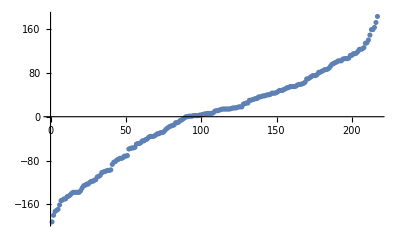

```mathematica
ListPlot[Drop[tradediffs,1][[All,2]]]
```

```mathematica
Join[Drop[tradediffs,1][[All,1]][[1;;9]]/."Marshall Islands"->None,Table[None,{Length[Drop[tradediffs,1]]-20}],Drop[tradediffs,1][[All,1]][[-10;;-1]]/."Sao Tome and Principe"->None/."French Polynesia"->None/."Seychelles"->None]
```

{Slovakia,Slovenia,Malta,Netherlands,Luxembourg,Malaysia,None,Lithuania,Ireland,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,China,None,Guatemala,New Zealand,None,Australia,Peru,Japan,United States of America,None}

```mathematica
plot1=ListPlot[Drop[tradediffs,1][[All,2]]->Join[Drop[tradediffs,1][[All,1]][[1;;9]]/."Marshall Islands"->None/."Lithuania"->None/."Malaysia"->None,Table[None,{Length[Drop[tradediffs,1]]-19}],Drop[tradediffs,1][[All,1]][[-10;;-1]]/."Sao Tome and Principe"->None/."French Polynesia"->None/."Seychelles"->None],ImageSize->Full,PlotRange->{{-50,250},{-230,230}},LabelingFunction->Automatic,PlotMarkers->Graphics[{PointSize[Medium],Point[{0,0}]}],LabelStyle->10]
```

-Graphics-

```mathematica
Export["appendix-joko-1.pdf",plot1]
```

appendix-joko-1.pdf

```mathematica
plot2=ListPlot[Drop[kofdiffs,1][[All,2]]->Join[Drop[kofdiffs,1][[All,1]][[1;;10]],Table[None,{Length[Drop[kofdiffs,1]]-20}],Drop[kofdiffs,1][[All,1]][[-10;;-1]]/."Haiti"->None/."Dominican Republic"->None/."Guatemala"->None],ImageSize->Full,PlotRange->{{-50,250},{-230,230}},LabelingFunction->Automatic,PlotMarkers->Graphics[{PointSize[Medium],Point[{0,0}]}],LabelStyle->10]
```

-Graphics-

```mathematica
Export["appendix-joko-2.pdf",plot2]
```

appendix-joko-2.pdf